```mathematica
p[{x_,y_}]:=A[[x,y]]
pic[L_]:=Graphics[{
Table[Line[{{0,i},{size,i}}],{i,0,size}],
Table[Line[{{i,0},{i,size}}],{i,0,size}],
Map[Rectangle[#,#-1]&,L]
},ImageSize->100]
```

```mathematica
f[L_]:=Module[{},
A=ReplacePart[Table[0,{size},{size}],L->1];
A=Transpose[Table[1,{4},{Length[A[[1]]]}]~Join~A~Join~Table[1,{4},{Length[A[[1]]]}]];
A=Transpose[Table[1,{4},{Length[A[[1]]]}]~Join~A~Join~Table[1,{4},{Length[A[[1]]]}]];

edges={};
stack={{{5,5},3}};
positions={stack[[1]]};
While[Length[stack]>0,
top=stack[[1]];
stack=Rest[stack];
state=Last[top];
pos=First[top];

If[state==1&&p[pos+{0,4}]==0,
t={pos+{0,4},3};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];
If[state==1&&p[pos+{0,-1}]==0,
t={pos+{0,-1},3};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];
If[state==1&&p[pos+{-1,0}]==0&&p[pos+{-1,1}]==0&&p[pos+{-1,2}]==0&&p[pos+{-1,3}]==0,
t={pos+{-1,0},1};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];If[state==1&&p[pos+{1,0}]==0&&p[pos+{1,1}]==0&&p[pos+{1,2}]==0&&p[pos+{1,3}]==0,
t={pos+{1,0},1};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];

If[state==2&&p[pos+{4,0}]==0,
t={pos+{4,0},3};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];
If[state==2&&p[pos+{-1,0}]==0,
t={pos+{-1,0},3};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];
If[state==2&&p[pos+{0,1}]==0&&p[pos+{1,1}]==0&&p[pos+{2,1}]==0&&p[pos+{3,1}]==0,
t={pos+{0,1},2};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];If[state==2&&p[pos+{0,-1}]==0&&p[pos+{1,-1}]==0&&p[pos+{2,-1}]==0&&p[pos+{3,-1}]==0,
t={pos+{0,-1},2};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];

If[state==3&&p[pos+{0,-1}]==0&&p[pos+{0,-2}]==0&&p[pos+{0,-3}]==0&&p[pos+{0,-4}]==0,
t={pos+{0,-4},1};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];
If[state==3&&p[pos+{0,1}]==0&&p[pos+{0,2}]==0&&p[pos+{0,3}]==0&&p[pos+{0,4}]==0,
t={pos+{0,1},1};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];
If[state==3&&p[pos+{-1,0}]==0&&p[pos+{-2,0}]==0&&p[pos+{-3,0}]==0&&p[pos+{-4,0}]==0,
t={pos+{-4,0},2};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];If[state==3&&p[pos+{1,0}]==0&&p[pos+{2,0}]==0&&p[pos+{3,0}]==0&&p[pos+{4,0}]==0,
t={pos+{1,0},2};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];

positions=Union[positions~Join~{top}]];
GraphPlot[edges,MultiedgeStyle->False,ImageSize->{600,300}]]
```

## generation

```mathematica
size=8;
```

```mathematica
minsize=40;
```

```mathematica
diameter:=Module[{},
vertices=Union[Flatten[Map[{#[[1]],#[[2]]}&,edges],1]];B=Table[0,{Length[vertices]},{Length[vertices]}];
For[i=1,i≤Length[edges],i++,
a=edges[[i,1]];
b=edges[[i,2]];
pa=Position[vertices,a][[1,1]];
pb=Position[vertices,b][[1,1]];
B=ReplacePart[B,{{pa,pb},{pb,pa}}->1]];
Clear[P];
P[1]=B;
P[i_]:=P[i]=Map[Sign,B.P[i-1]+P[i-1],2];
For[i=minsize,i≤Length[vertices+1],i++,
If[Union[Flatten[P[i]-P[i-1]]]=={0},Return[i-1];Break[]]]]
```

```mathematica
all[L_]:=(f[L];d=diameter;Print[pic[L]];Print[d];Print[f[L]])
```

```mathematica
For[m=1,m>0,m++,
L={};
blocks=RandomInteger[{5,10}];
While[Length[L]<blocks,
a=RandomInteger[{1,size}];b=RandomInteger[{1,size}];
While[a<2&&b<2,a=RandomInteger[{1,size}];b=RandomInteger[{1,size}]];
L=Union[L~Join~{{a,b}}]];
f[L];d=diameter;
If[d≥minsize,Print[pic[L]];Print[d];Print[f[L]]]]
```

## possibility

-Graphics-

52

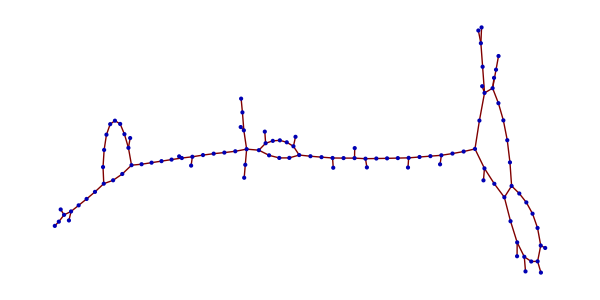

-Graphics-

52

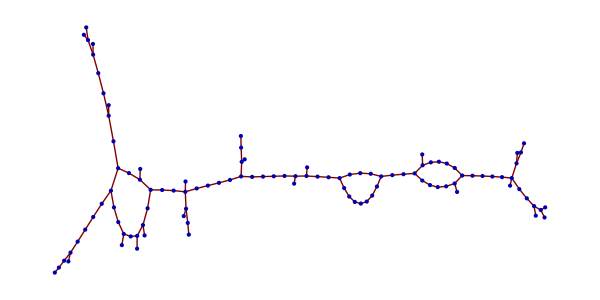

-Graphics-

42

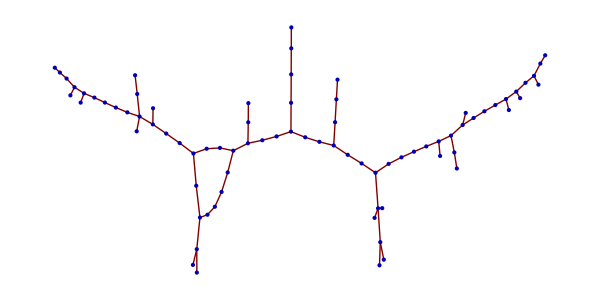

-Graphics-

43

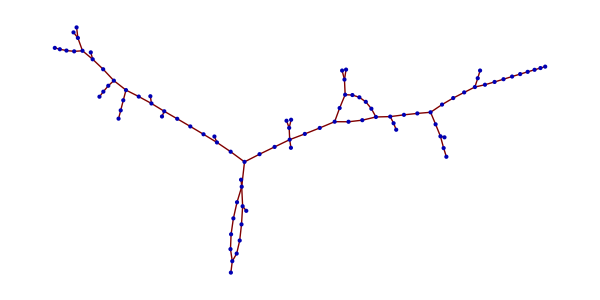

-Graphics-

45

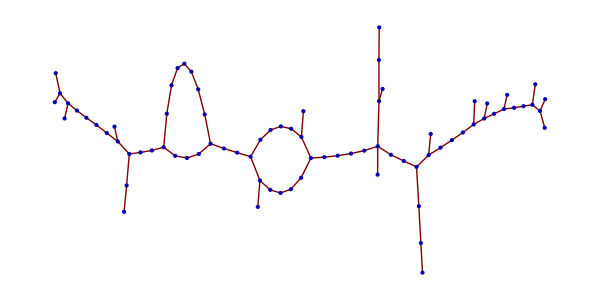

-Graphics-

47

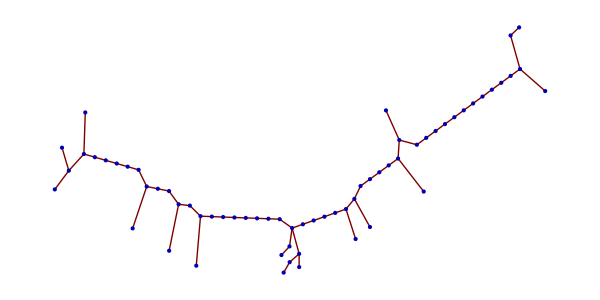

-Graphics-

43

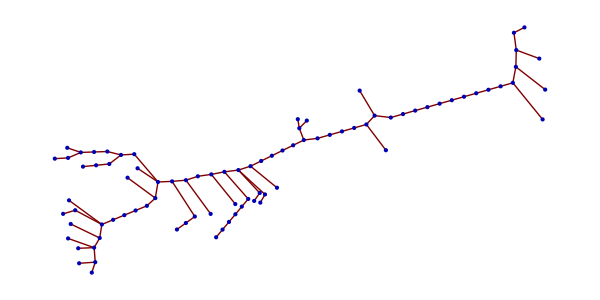

-Graphics-

44

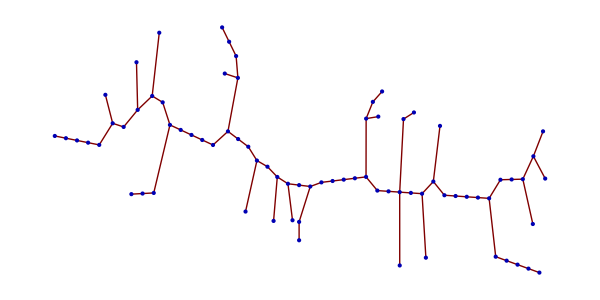

-Graphics-

43

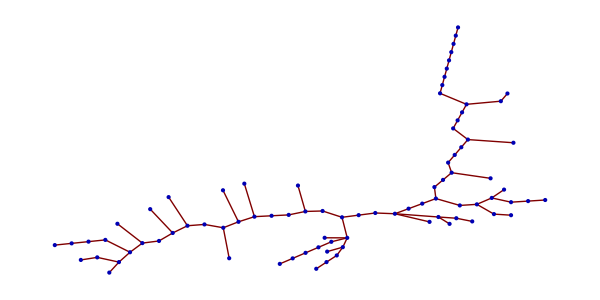

-Graphics-

40

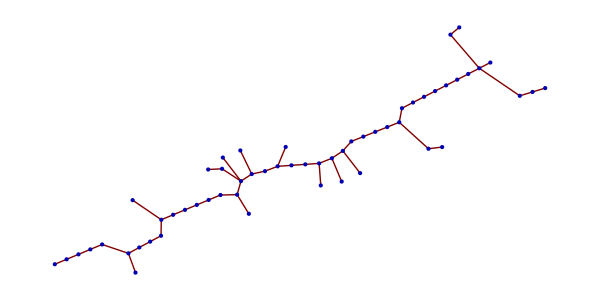

-Graphics-

44

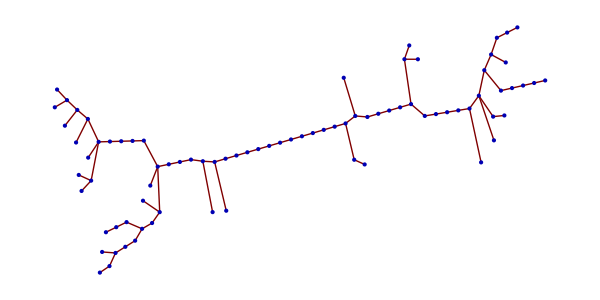

-Graphics-

43

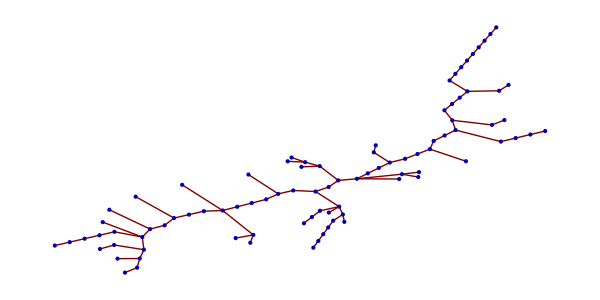

-Graphics-

43

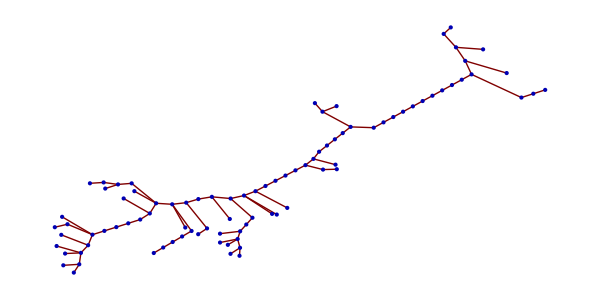

-Graphics-

41

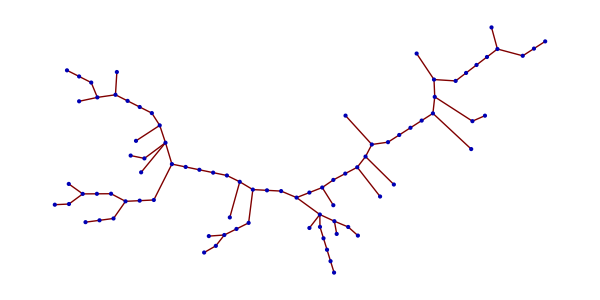

-Graphics-

42

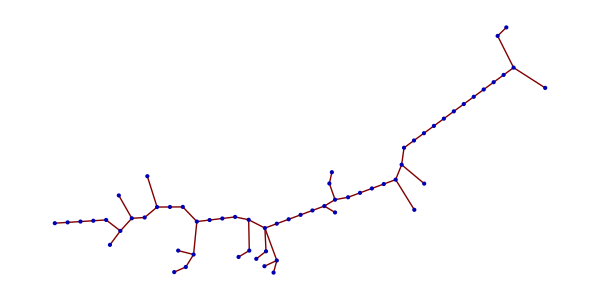

-Graphics-

42

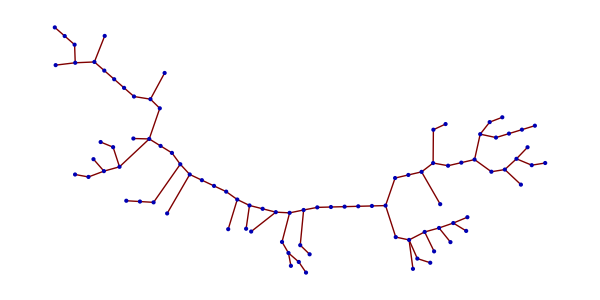

-Graphics-

43

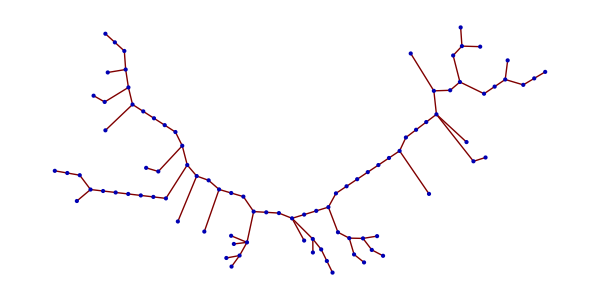

-Graphics-

45

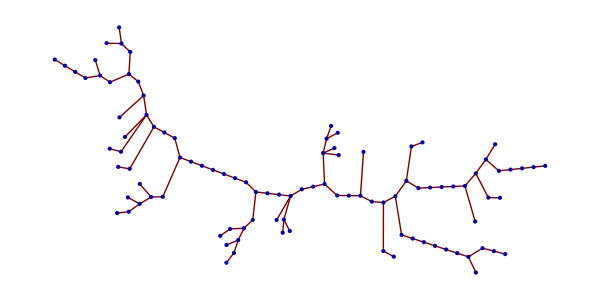

-Graphics-

43

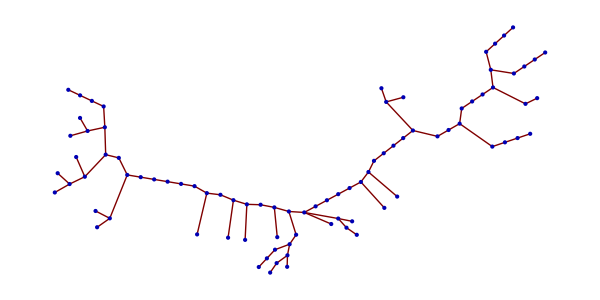

-Graphics-

41

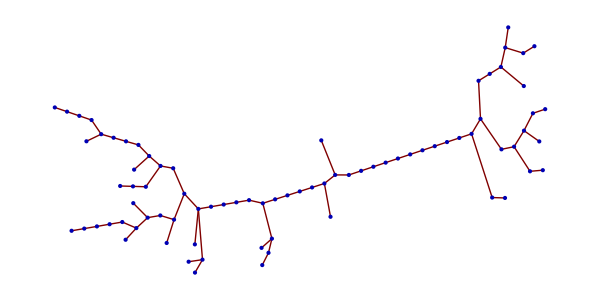

-Graphics-

51

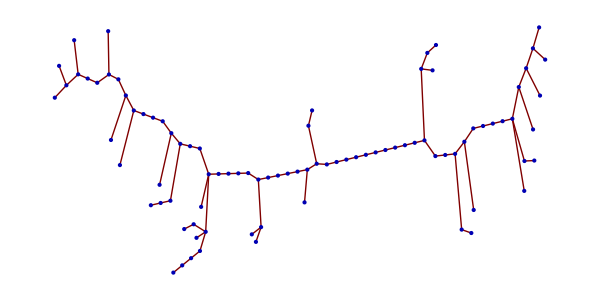

-Graphics-

45

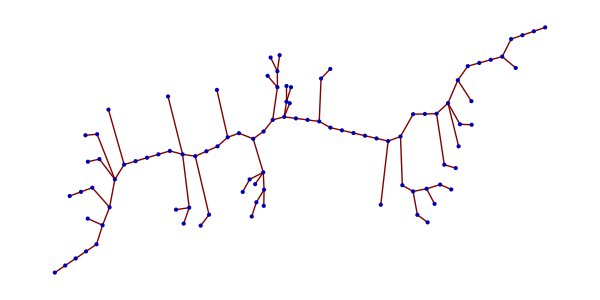

-Graphics-

40

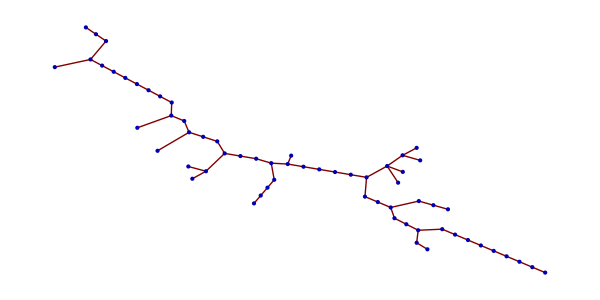

-Graphics-

40

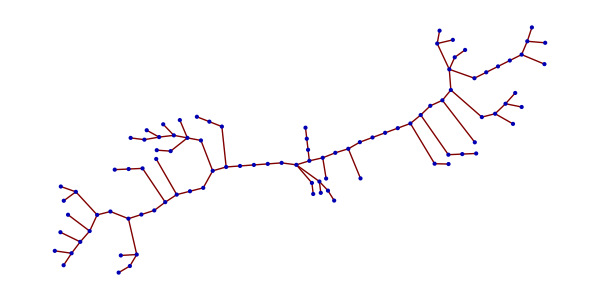

-Graphics-

43

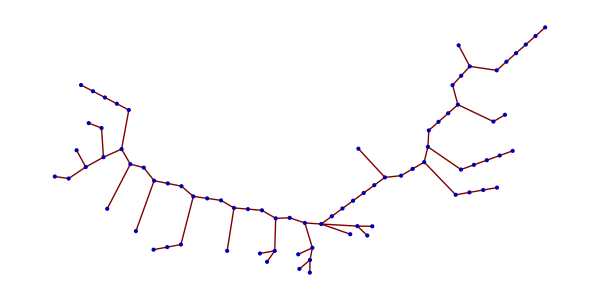

-Graphics-

46

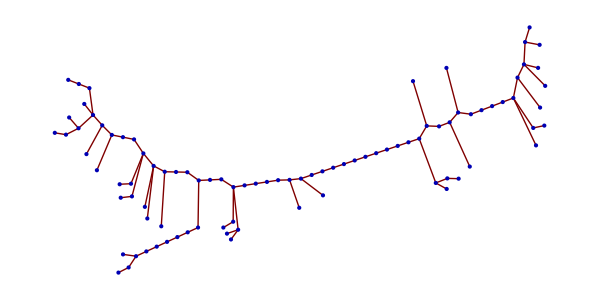

-Graphics-

43

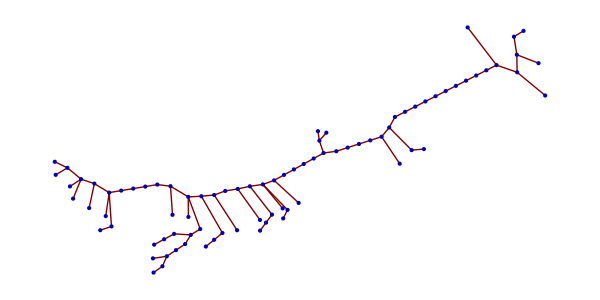

-Graphics-

41

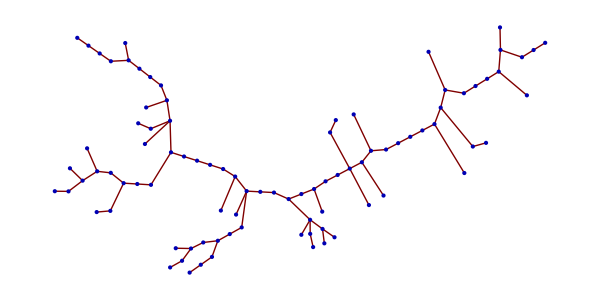

-Graphics-

40